# Masterthesis Plots

Define plot style

```mathematica
defaultPlotOptions:={ImageSize->Medium,BaseStyle->{FontFamily->"Latin Modern Math"},PlotTheme->{"Frame","Vibrant","Grid"}};
```

Discrete (sampled) sine

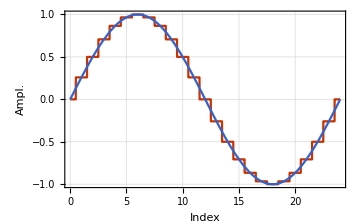

```mathematica
nn=24;
lookupPlot=Plot[{Sin[Round[t]/nn 2Pi],Sin[t/nn*2Pi]},{t,0,nn},Evaluate@defaultPlotOptions,
Exclusions->None,FrameTicks->{{Automatic,Automatic},{Automatic,Table[{i,(2Pi*i)/nn},{i,0,nn,nn/4}]}},FrameLabel->{"Index","Ampl."}]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/table-lookup.pdf",lookupPlot,"PDF"];
```

```mathematica
ColorFunction->Function[{x,y},Hue[y]]
```

ColorFunction→Function[{x,y},Hue[y]]

Sine wave spectrum

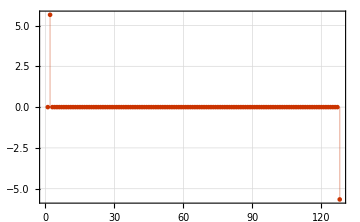

```mathematica
ListPlot[Im[Fourier[Table[N[Sin[t/n*2Pi]],{t,0,n-1}]]],PlotRange->Full,Filling->Axis,Evaluate@defaultPlotOptions]
```

Wavetable and spectrum

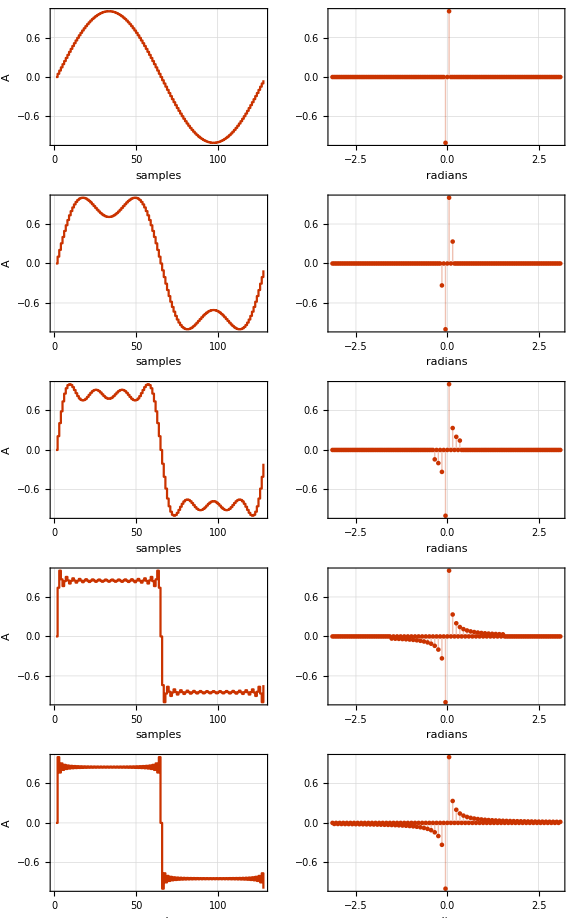

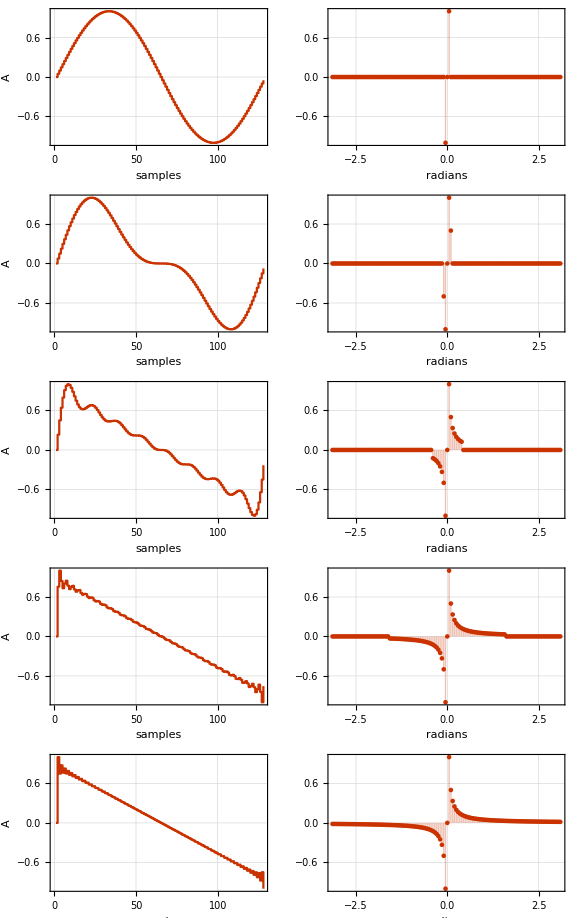

```mathematica
n=128;
sr=64;
dt=1/sr;
df=sr/n;
saw[h_]:=RotateRight[Table[If[k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
sqr[h_]:=RotateRight[Table[If[EvenQ[k]||k==0||Abs[k]>h,0,I/k],{k,-n/2,n/2-1}],n/2];
(* the zeroth element of a list contains its type *)
radians=2 Pi/n Range[-n/2,n/2-1];
plotsSaw =Table[{
ListLinePlot[2Rescale[Re[InverseFourier[saw[k]]]]-1,PlotRange->{{0,n},{-1,1}},InterpolationOrder->0,FrameLabel->{"samples","A"},Evaluate@defaultPlotOptions],
ListPlot[MapThread[List,{radians,Im[RotateRight[saw[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},Evaluate@defaultPlotOptions]
},{k,{1,2,8,n/4,n}}];
plotsSquare =Table[{
ListLinePlot[2Rescale[Re[InverseFourier[sqr[k]]]]-1,PlotRange->Full,InterpolationOrder->0,FrameLabel->{"samples","A"},Evaluate@defaultPlotOptions],
ListPlot[MapThread[List,{radians,Im[RotateRight[sqr[k],n/2]]}],PlotRange->Full, Filling->Axis,FrameLabel->{"radians"},Evaluate@defaultPlotOptions]
},{k,{1,4,8,n/4,n}}];
sqrPlot=Show[GraphicsGrid[plotsSquare,Frame->False,ImageSize->Large]]
sawPlot=Show[GraphicsGrid[plotsSaw,Frame->False,ImageSize->Large]]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/sqr-table.pdf",sqrPlot,"PDF"];
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/saw-table.pdf",sawPlot,"PDF"];
```

Ration between input levels and db scale

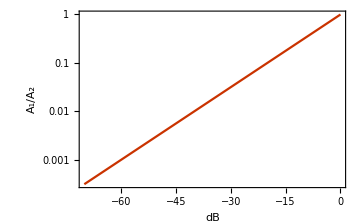

```mathematica
dB[lev_] := 20 Log10[lev/1];
dbPlot=LogPlot[10^(d/20),{d,0,-70},PlotRange->{{0,-70},{0,1}},FrameLabel->{"dB","A_1/A_2"}, RotateLabel->False,Evaluate@defaultPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/db.pdf",dbPlot,"PDF"];
```

Table Interpolation

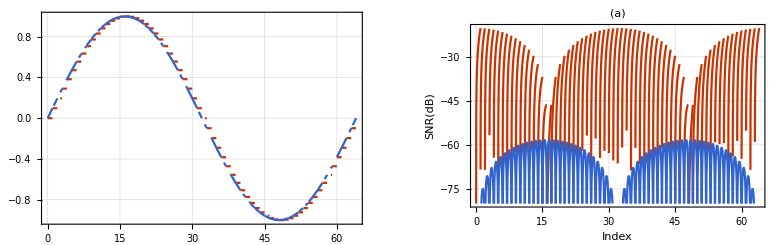

-28.0471

-20.3103

-64.125

-58.394

```mathematica
nn=64; (* Nr. of samples *)
s[n_]:=Sin[n/nn*2Pi];(* pure sine *)
sRound[n_]:=Sin[Floor[n]/nn*2Pi]; (* sine zero-degree interpolation *)
sInt[n_]:=s[Floor[n]]+(s[Floor[n]+1]-s[Floor[n]])(n-Floor[n]);(* sine with linear interpolation *)

p1=Plot[{sRound[x],sInt[x]},{x,0,nn},
PlotRange->{{0,nn},{-1,1}},Evaluate@defaultPlotOptions];
(* error plot *)
p2=Plot[{dB[Abs[s[x]-sRound[x]]],dB[Abs[s[x]-sInt[x]]]},{x,0,nn},PlotRange->{{0,nn},{0,-80}},FrameLabel->{"Index","SNR(dB)"},Evaluate@defaultPlotOptions,PlotLabel->"(a)"];
GraphicsRow[{p1,p2}]
t1:=Table[s[n]-sRound[n]//N,{n,0,nn,1/nn}];
t2:=Table[s[n]-sInt[n]//N,{n,0,nn,1/nn}]; 
dB[RootMeanSquare[t1]]
dB[Max[t1]]
dB[RootMeanSquare[t2]]
dB[Max[t2]]
```

Aliasing

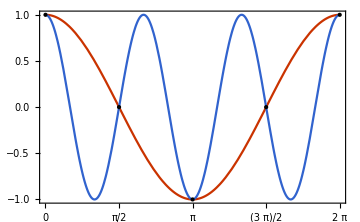

```mathematica
aliasPlot=Plot[{Cos[x],Cos[3x]},{x,0,2Pi},GridLines->{{Pi,2Pi},{-1,-.5,0,.5,1}},Epilog->{PointSize->Large,Point[Table[{n ,Cos[n]},{n,0,2Pi,Pi/2}]]},
FrameTicks->{{Automatic,Automatic},{Table[n,{n,0,2Pi,Pi/2}],Automatic}},Evaluate@defaultPlotOptions]
Export["/home/andreas/personal/edu/Uni-Leipzig/Masterarbeit/thesis/doc/imgs/aliasing.pdf",aliasPlot,"PDF"];
```